```mathematica
SetDirectory["C:\\Users\\cefit\\source\\repos\\Two_Electron_Phonon_Relaxation\\Two_Electron_Phonon_Relaxation"]
```

C:\Users\cefit\source\repos\Two_Electron_Phonon_Relaxation\Two_Electron_Phonon_Relaxation

```mathematica
data = Import["relaxation.txt", "Table"]
```

{{2,2215.78},{2.00833,2197.46},{2.01667,2179.24},{2.025,2161.13},{2.03333,2143.11},{2.04167,2125.19},{2.05,2107.38},{2.05833,2089.66},{2.06667,2072.04},{2.075,2054.53},{2.08333,2037.11},{2.09167,2019.79},{2.1,2002.57},{2.10833,1985.44},{2.11667,1968.42},{2.125,1951.49},{2.13333,1934.66},{2.14167,1917.93},{2.15,1901.29},{2.15833,1884.75},{2.16667,1868.31},{2.175,1851.96},{2.18333,1835.71},{2.19167,1819.55},{2.2,1803.49},{2.20833,1787.52},{2.21667,1771.65},{2.225,1755.87},{2.23333,1740.19},{2.24167,1724.6},{2.25,1709.1},{2.25833,1693.7},{2.26667,1678.38},{2.275,1663.17},{2.28333,1648.04},{2.29167,1633},{2.3,1618.06},{2.30833,1603.21},{2.31667,1588.45},{2.325,1573.78},{2.33333,1559.2},{2.34167,1544.71},{2.35,1530.32},{2.35833,1516.01},{2.36667,1501.79},{2.375,1487.66},{2.38333,1473.62},{2.39167,1459.67},{2.4,1445.8},{2.40833,1432.03},{2.41667,1418.34},{2.425,1404.74},{2.43333,1391.22},{2.44167,1377.8},{2.45,1364.46},{2.45833,1351.2},{2.46667,1338.04},{2.475,1324.96},{2.48333,1311.96},{2.49167,1299.05},{2.5,1286.22},{2.50833,1273.48},{2.51667,1260.83},{2.525,1248.25},{2.53333,1235.76},{2.54167,1223.36},{2.55,1211.04},{2.55833,1198.8},{2.56667,1186.64},{2.575,1174.57},{2.58333,1162.58},{2.59167,1150.67},{2.6,1138.84},{2.60833,1127.09},{2.61667,1115.43},{2.625,1103.84},{2.63333,1092.34},{2.64167,1080.92},{2.65,1069.57},{2.65833,1058.31},{2.66667,1047.12},{2.675,1036.02},{2.68333,1024.99},{2.69167,1014.04},{2.7,1003.17},{2.70833,992.378},{2.71667,981.664},{2.725,971.026},{2.73333,960.466},{2.74167,949.983},{2.75,939.576},{2.75833,929.246},{2.76667,918.991},{2.775,908.812},{2.78333,898.709},{2.79167,888.681},{2.8,878.728},{2.80833,868.849},{2.81667,859.044},{2.825,849.314},{2.83333,839.657},{2.84167,830.074},{2.85,820.564},{2.85833,811.127},{2.86667,801.763},{2.875,792.471},{2.88333,783.251},{2.89167,774.103},{2.9,765.026},{2.90833,756.021},{2.91667,747.086},{2.925,738.222},{2.93333,729.429},{2.94167,720.706},{2.95,712.052},{2.95833,703.468},{2.96667,694.954},{2.975,686.508},{2.98333,678.131},{2.99167,669.822},{3,661.582},{3.00833,653.409},{3.01667,645.304},{3.025,637.267},{3.03333,629.296},{3.04167,621.392},{3.05,613.555},{3.05833,605.784},{3.06667,598.078},{3.075,590.438},{3.08333,582.864},{3.09167,575.355},{3.1,567.91},{3.10833,560.53},{3.11667,553.214},{3.125,545.962},{3.13333,538.774},{3.14167,531.649},{3.15,524.587},{3.15833,517.588},{3.16667,510.652},{3.175,503.778},{3.18333,496.965},{3.19167,490.215},{3.2,483.526},{3.20833,476.898},{3.21667,470.33},{3.225,463.824},{3.23333,457.378},{3.24167,450.991},{3.25,444.665},{3.25833,438.398},{3.26667,432.19},{3.275,426.04},{3.28333,419.95},{3.29167,413.918},{3.3,407.944},{3.30833,402.027},{3.31667,396.169},{3.325,390.367},{3.33333,384.622},{3.34167,378.934},{3.35,373.302},{3.35833,367.727},{3.36667,362.207},{3.375,356.742},{3.38333,351.333},{3.39167,345.979},{3.4,340.679},{3.40833,335.434},{3.41667,330.243},{3.425,325.106},{3.43333,320.023},{3.44167,314.992},{3.45,310.015},{3.45833,305.09},{3.46667,300.218},{3.475,295.398},{3.48333,290.63},{3.49167,285.913},{3.5,281.248},{3.50833,276.634},{3.51667,272.07},{3.525,267.557},{3.53333,263.094},{3.54167,258.681},{3.55,254.318},{3.55833,250.004},{3.56667,245.739},{3.575,241.523},{3.58333,237.355},{3.59167,233.236},{3.6,229.165},{3.60833,225.141},{3.61667,221.164},{3.625,217.235},{3.63333,213.352},{3.64167,209.516},{3.65,205.727},{3.65833,201.983},{3.66667,198.285},{3.675,194.632},{3.68333,191.025},{3.69167,187.462},{3.7,183.944},{3.70833,180.47},{3.71667,177.041},{3.725,173.655},{3.73333,170.312},{3.74167,167.013},{3.75,163.756},{3.75833,160.542},{3.76667,157.371},{3.775,154.241},{3.78333,151.153},{3.79167,148.107},{3.8,145.102},{3.80833,142.138},{3.81667,139.214},{3.825,136.331},{3.83333,133.488},{3.84167,130.685},{3.85,127.921},{3.85833,125.197},{3.86667,122.511},{3.875,119.864},{3.88333,117.256},{3.89167,114.685},{3.9,112.153},{3.90833,109.658},{3.91667,107.2},{3.925,104.78},{3.93333,102.396},{3.94167,100.048},{3.95,97.7369},{3.95833,95.4614},{3.96667,93.2216},{3.975,91.017},{3.98333,88.8475},{3.99167,86.7127},{4,84.6124},{4.00833,82.5463},{4.01667,80.5141},{4.025,78.5155},{4.03333,76.5503},{4.04167,74.6182},{4.05,72.7188},{4.05833,70.852},{4.06667,69.0173},{4.075,67.2147},{4.08333,65.4436},{4.09167,63.704},{4.1,61.9955},{4.10833,60.3178},{4.11667,58.6706},{4.125,57.0538},{4.13333,55.4668},{4.14167,53.9096},{4.15,52.3819},{4.15833,50.8832},{4.16667,49.4134},{4.175,47.9722},{4.18333,46.5593},{4.19167,45.1744},{4.2,43.8173},{4.20833,42.4876},{4.21667,41.1851},{4.225,39.9095},{4.23333,38.6604},{4.24167,37.4378},{4.25,36.2412},{4.25833,35.0703},{4.26667,33.925},{4.275,32.8048},{4.28333,31.7096},{4.29167,30.6391},{4.3,29.5929},{4.30833,28.5708},{4.31667,27.5725},{4.325,26.5978},{4.33333,25.6463},{4.34167,24.7177},{4.35,23.8119},{4.35833,22.9284},{4.36667,22.0671},{4.375,21.2276},{4.38333,20.4097},{4.39167,19.6131},{4.4,18.8375},{4.40833,18.0826},{4.41667,17.3481},{4.425,16.6338},{4.43333,15.9394},{4.44167,15.2646},{4.45,14.6091},{4.45833,13.9726},{4.46667,13.3549},{4.475,12.7557},{4.48333,12.1747},{4.49167,11.6116},{4.5,11.0661},{4.50833,10.538},{4.51667,10.027},{4.525,9.53275},{4.53333,9.05502},{4.54167,8.59352},{4.55,8.14798},{4.55833,7.71811},{4.56667,7.30363},{4.575,6.90426},{4.58333,6.51973},{4.59167,6.14974},{4.6,5.79402},{4.60833,5.45229},{4.61667,5.12427},{5.41667,5.21951},{5.425,5.55154},{5.43333,5.89736},{5.44167,6.25726},{5.45,6.6315},{5.45833,7.02038},{5.46667,7.42417},{5.475,7.84316},{5.48333,8.27761},{5.49167,8.72783},{5.5,9.19408},{5.50833,9.67664},{5.51667,10.1758},{5.525,10.6918},{5.53333,11.225},{5.54167,11.7757},{5.55,12.344},{5.55833,12.9304},{5.56667,13.535},{5.575,14.1582},{5.58333,14.8002},{5.59167,15.4614},{5.6,16.142},{5.60833,16.8422},{5.61667,17.5624},{5.625,18.3029},{5.63333,19.0638},{5.64167,19.8456},{5.65,20.6485},{5.65833,21.4727},{5.66667,22.3186},{5.675,23.1864},{5.68333,24.0764},{5.69167,24.9889},{5.7,25.9242},{5.70833,26.8825},{5.71667,27.8642},{5.725,28.8695},{5.73333,29.8986},{5.74167,30.952},{5.75,32.0297},{5.75833,33.1323},{5.76667,34.2598},{5.775,35.4126},{5.78333,36.591},{5.79167,37.7953},{5.8,39.0257},{5.80833,40.2825},{5.81667,41.566},{5.825,42.8765},{5.83333,44.2143},{5.84167,45.5796},{5.85,46.9727},{5.85833,48.3939},{5.86667,49.8435},{5.875,51.3218},{5.88333,52.829},{5.89167,54.3654},{5.9,55.9313},{5.90833,57.527},{5.91667,59.1528},{5.925,60.8089},{5.93333,62.4957},{5.94167,64.2133},{5.95,65.9622},{5.95833,67.7425},{5.96667,69.5546},{5.975,71.3986},{5.98333,73.275},{5.99167,75.184},{6,77.1259},{6.00833,79.1009},{6.01667,81.1094},{6.025,83.1515},{6.03333,85.2277},{6.04167,87.3381},{6.05,89.4831},{6.05833,91.6629},{6.06667,93.8778},{6.075,96.1282},{6.08333,98.4142},{6.09167,100.736},{6.1,103.094},{6.10833,105.489},{6.11667,107.921},{6.125,110.389},{6.13333,112.895},{6.14167,115.439},{6.15,118.02},{6.15833,120.64},{6.16667,123.298},{6.175,125.995},{6.18333,128.731},{6.19167,131.507},{6.2,134.322},{6.20833,137.176},{6.21667,140.071},{6.225,143.007},{6.23333,145.983},{6.24167,149},{6.25,152.059},{6.25833,155.159},{6.26667,158.301},{6.275,161.485},{6.28333,164.711},{6.29167,167.98},{6.3,171.292},{6.30833,174.648},{6.31667,178.047},{6.325,181.489},{6.33333,184.976},{6.34167,188.507},{6.35,192.083},{6.35833,195.704},{6.36667,199.37},{6.375,203.081},{6.38333,206.839},{6.39167,210.642},{6.4,214.492},{6.40833,218.388},{6.41667,222.331},{6.425,226.321},{6.43333,230.359},{6.44167,234.445},{6.45,238.578},{6.45833,242.76},{6.46667,246.991},{6.475,251.27},{6.48333,255.599},{6.49167,259.977},{6.5,264.404},{6.50833,268.882},{6.51667,273.41},{6.525,277.988},{6.53333,282.617},{6.54167,287.298},{6.55,292.029},{6.55833,296.813},{6.56667,301.648},{6.575,306.536},{6.58333,311.476},{6.59167,316.469},{6.6,321.515},{6.60833,326.614},{6.61667,331.767},{6.625,336.974},{6.63333,342.235},{6.64167,347.551},{6.65,352.921},{6.65833,358.347},{6.66667,363.827},{6.675,369.364},{6.68333,374.956},{6.69167,380.604},{6.7,386.309},{6.70833,392.07},{6.71667,397.889},{6.725,403.765},{6.73333,409.698},{6.74167,415.689},{6.75,421.738},{6.75833,427.846},{6.76667,434.013},{6.775,440.238},{6.78333,446.523},{6.79167,452.867},{6.8,459.271},{6.80833,465.735},{6.81667,472.259},{6.825,478.844},{6.83333,485.49},{6.84167,492.197},{6.85,498.966},{6.85833,505.797},{6.86667,512.689},{6.875,519.644},{6.88333,526.661},{6.89167,533.742},{6.9,540.885},{6.90833,548.092},{6.91667,555.363},{6.925,562.698},{6.93333,570.097},{6.94167,577.561},{6.95,585.089},{6.95833,592.683},{6.96667,600.342},{6.975,608.066},{6.98333,615.857},{6.99167,623.714},{7,631.638},{7.00833,639.628},{7.01667,647.686},{7.025,655.81},{7.03333,664.003},{7.04167,672.263},{7.05,680.592},{7.05833,688.989},{7.06667,697.455},{7.075,705.99},{7.08333,714.595},{7.09167,723.269},{7.1,732.013},{7.10833,740.827},{7.11667,749.711},{7.125,758.667},{7.13333,767.693},{7.14167,776.791},{7.15,785.96},{7.15833,795.201},{7.16667,804.515},{7.175,813.9},{7.18333,823.359},{7.19167,832.89},{7.2,842.495},{7.20833,852.173},{7.21667,861.925},{7.225,871.752},{7.23333,881.652},{7.24167,891.628},{7.25,901.678},{7.25833,911.804},{7.26667,922.005},{7.275,932.282},{7.28333,942.634},{7.29167,953.064},{7.3,963.57},{7.30833,974.153},{7.31667,984.813},{7.325,995.55},{7.33333,1006.37},{7.34167,1017.26},{7.35,1028.23},{7.35833,1039.28},{7.36667,1050.41},{7.375,1061.62},{7.38333,1072.91},{7.39167,1084.27},{7.4,1095.72},{7.40833,1107.25},{7.41667,1118.86},{7.425,1130.55},{7.43333,1142.32},{7.44167,1154.17},{7.45,1166.1},{7.45833,1178.12},{7.46667,1190.22},{7.475,1202.4},{7.48333,1214.66},{7.49167,1227.01},{7.5,1239.44},{7.50833,1251.95},{7.51667,1264.55},{7.525,1277.23},{7.53333,1289.99},{7.54167,1302.84},{7.55,1315.78},{7.55833,1328.8},{7.56667,1341.91},{7.575,1355.1},{7.58333,1368.38},{7.59167,1381.74},{7.6,1395.2},{7.60833,1408.74},{7.61667,1422.36},{7.625,1436.08},{7.63333,1449.88},{7.64167,1463.77},{7.65,1477.75},{7.65833,1491.81},{7.66667,1505.97},{7.675,1520.21},{7.68333,1534.55},{7.69167,1548.97},{7.7,1563.49},{7.70833,1578.09},{7.71667,1592.79},{7.725,1607.58},{7.73333,1622.46},{7.74167,1637.42},{7.75,1652.49},{7.75833,1667.64},{7.76667,1682.89},{7.775,1698.22},{7.78333,1713.66},{7.79167,1729.18},{7.8,1744.8},{7.80833,1760.51},{7.81667,1776.32},{7.825,1792.22},{7.83333,1808.21},{7.84167,1824.3},{7.85,1840.49},{7.85833,1856.77},{7.86667,1873.14},{7.875,1889.61},{7.88333,1906.18},{7.89167,1922.85},{7.9,1939.61},{7.90833,1956.47},{7.91667,1973.42},{7.925,1990.48},{7.93333,2007.63},{7.94167,2024.88},{7.95,2042.23},{7.95833,2059.68},{7.96667,2077.22},{7.975,2094.87},{7.98333,2112.62},{7.99167,2130.46},{8,2148.41}}

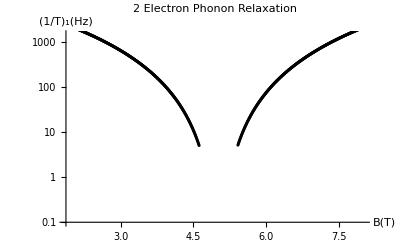

```mathematica
ListLogPlot[Transpose[Thread[{First[#],Rest[#]}]&/@data] , AxesLabel->{"B(T)", "\!\(\*SubscriptBox[\(1/T\), \(1\)]\)(Hz)"},PlotLegends->Automatic, PlotRange->{Automatic,{0.1, 1500}},PlotStyle->{{Solid, Black}, {Dashed, Red}, {Dashed, Blue}} ,PlotLabel->"2 Electron Phonon Relaxation"]
```